## Preamble

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
$Version
```

12.2.0 for Mac OS X x86 (64-bit) (December 12, 2020)

```mathematica
(* speed of light in km/s *)
cc=299792458/1000;

(* auxiliary cosmographic function *)
fcg[z_,q0_,j0_]:= Log10[1+(1-q0)/2 z-(1-q0-3q0^2+j0)/6 z^2]+Log10[cc z];

(* apparent magnitude *)
mB[z_,H0_,q0_,j0_,MB_]:=5 fcg[z,q0,j0]+25+MB-5Log10[H0];
```

## Supercal data analysis (can be skipped)

### preparing data

```mathematica
Hyperlink["Link to supercal data", "https://github.com/sfeeney/hh0"]
```

[Link to supercal data](https://github.com/sfeeney/hh0)

```mathematica
Dimensions[headsc=Import["data/supercal_vH0.fitres.txt","Table"][[12,2;;]]];
Dimensions[datasc=Import["data/supercal_vH0.fitres.txt","Table","HeaderLines"->14][[All,2;;]]]

(* fixing names *)
sdss={16314,16392,16333,14318,17186,17784,7876};
truname={"2006oa","2006ob","2006on","2006py","2007hx","2007jg","2005ir"};
Do[
datasc[[All,1]]=If[#==sdss[[i]],truname[[i]],#]&/@datasc[[All,1]];
,{i,Length[sdss]}];

(* correcting the apparent magnitude according to the host galaxy mass *)
Do[
Which[
datasc[[i,10]]≥10
,
datasc[[i,21]]+=0.03
,
0≤datasc[[i,10]]<10
,
datasc[[i,21]]-=0.03
,
datasc[[i,10]]<0
,
Null;
];
,{i,Length[datasc]}]

TableForm[Prepend[datasc[[;;15]],Range[Length[headsc]]],TableHeadings->{None,headsc}]
```

{1096,41}

CID | CIDint | IDSURVEY | TYPE | FIELD | zHD | zHDERR | z | zERR | HOST_LOGMASS | HOST_LOGMASS_ERR | SNRMAX1 | SNRMAX2 | SNRMAX3 | PKMJD | PKMJDERR | x1 | x1ERR | c | cERR | mB | mBERR | x0 | x0ERR | COV_x1_c | COV_x1_x0 | COV_c_x0 | NDOF | FITCHI2 | FITPROB | RA | DECL | TGAPMAX | MU | MUERR | MUERR_NOSIGMB | MURES | MUPULL | sbar | cbar | ERRCODE
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41
744 | 744 | 1 | 120 | 82N | 0.12694 | 0.00001 | 0.12825 | 0.00001 | 10.47 | 0.075 | 43.4159 | 37.426 | 22.5996 | 53612.9 | 0.767 | 1.3867 | 0.3155 | 0.0657977 | 0.0337941 | 19.5667 | 0.057606 | 0.000274996 | 0.0000149845 | 0.000715994 | 1.30979×10^-7 | -4.02726×10^-7 | 31 | 20.6747 | 0.9385 | -30.8016 | 0.317392 | 0.317392 | 38.854 | 0.0762 | 0.0762 | -0.041 | -0.533 | 1.467 | 0.052 | 0
1112 | 1112 | 1 | 120 | 82S | 0.25609 | 0.00001 | 0.25761 | 0.00001 | 11.351 | 0.059 | 13.3437 | 11.859 | 8.472 | 53630.1 | 0.698 | -0.605076 | 0.7174 | -0.0254581 | 0.0532075 | 21.2929 | 0.0657151 | 0.0000560832 | 3.49932×10^-6 | 0.00627207 | -1.37776×10^-6 | -9.32217×10^-8 | 43 | 26.9626 | 0.9734 | -20.9824 | -0.375273 | -0.375273 | 40.5843 | 0.1809 | 0.1809 | 0.009 | 0.051 | -0.625 | -0.024 | 0
1241 | 1241 | 1 | 120 | 82S | 0.08848 | 0.00001 | 0.08979 | 0.00001 | 10.696 | 0.103 | 63.8605 | 54.282 | 40.1992 | 53635.4 | 0.078 | -0.541778 | 0.0789597 | 0.0502601 | 0.0238546 | 18.8809 | 0.0452172 | 0.000517156 | 0.000022054 | 0.0000606139 | -2.82776×10^-7 | -3.98893×10^-7 | 56 | 52.3885 | 0.6124 | -22.3275 | -0.776637 | -0.776637 | 37.9465 | 0.0515 | 0.0515 | -0.119 | -2.303 | -0.484 | 0.009 | 0
1371 | 1371 | 1 | 120 | 82S | 0.11797 | 0.00001 | 0.11934 | 0.00001 | 10.893 | 0.067 | 63.8619 | 38.7701 | 38.7632 | 53633.3 | 0.107 | 0.7898 | 0.0969753 | -0.0995807 | 0.0213383 | 18.7855 | 0.0361471 | 0.000564647 | 0.0000186649 | 0.0000942886 | -3.40096×10^-7 | -2.90445×10^-7 | 55 | 72.203 | 0.0597296 | -10.6263 | 0.429294 | 0.429294 | 38.502 | 0.0499 | 0.0499 | -0.224 | -4.486 | 0.942 | -0.176 | 0
1580 | 1580 | 1 | 120 | 82S | 0.18322 | 0.00001 | 0.184 | 0.00001 | 10.75 | 0.04 | 27.1215 | 23.5785 | 16.6583 | 53634. | 0.282 | 0.8981 | 0.2454 | -0.040732 | 0.0312441 | 20.0274 | 0.0701723 | 0.000179903 | 0.0000118706 | 0.00046935 | -6.67×10^-7 | -2.70149×10^-7 | 67 | 30.1352 | 1 | 45.323 | -0.644123 | -0.644123 | 39.5766 | 0.0794 | 0.0794 | -0.177 | -2.228 | 1.209 | -0.078 | 0
1794 | 1794 | 1 | 120 | 82N | 0.1407 | 0.00001 | 0.14191 | 0.00001 | 9.27 | 0.076 | 41.7464 | 30.9997 | 22.5872 | 53624.7 | 0.55 | 1.1683 | 0.3208 | 0.0319205 | 0.0290618 | 19.7854 | 0.0572016 | 0.000212742 | 0.0000114123 | 0.000367101 | -2.93294×10^-8 | -2.45773×10^-7 | 44 | 34.7437 | 0.8653 | -42.1633 | -0.445407 | -0.445407 | 39.2072 | 0.074 | 0.074 | 0.074 | 0.998 | 0.99 | 0.049 | 0
2031 | 2031 | 1 | 120 | 82S | 0.15186 | 0.00001 | 0.153 | 0.00001 | 9.204 | 54.124 | 57.1365 | 45.2261 | 27.1193 | 53636.9 | 0.14 | 0.4851 | 0.1436 | -0.128238 | 0.0238852 | 19.3507 | 0.046458 | 0.000317473 | 0.000013473 | 0.000017857 | -2.3686×10^-7 | -2.27054×10^-7 | 53 | 62.9586 | 0.1644 | -47.9569 | -1.17149 | -1.17149 | 39.1734 | 0.0584 | 0.0584 | -0.138 | -2.372 | 0.634 | -0.169 | 0
2102 | 2102 | 1 | 120 | 82S | 0.09401 | 0.00001 | 0.0951 | 0.00001 | 11.018 | 53.937 | 98.6983 | 72.379 | 41.7482 | 53620.2 | 0.503 | 1.2641 | 0.1957 | -0.10776 | 0.0246565 | 18.3832 | 0.0572439 | 0.000817952 | 0.0000430407 | -0.000795013 | 1.33621×10^-6 | -8.18819×10^-7 | 39 | 37.0163 | 0.5607 | -47.7791 | 0.191053 | 0.191053 | 38.1914 | 0.0575 | 0.0575 | -0.006 | -0.11 | 1.278 | -0.11 | 0
2165 | 2165 | 1 | 120 | 82N | 0.28662 | 0.00001 | 0.288 | 0.00001 | 9.485 | 0.186 | 14.8102 | 11.8634 | 7.877 | 53634.4 | 0.487 | 0.5222 | 0.582 | -0.122535 | 0.0440305 | 21.2389 | 0.0518001 | 0.0000557717 | 2.56915×10^-6 | 0.00580952 | -9.06416×10^-7 | -5.93956×10^-8 | 64 | 33.4988 | 0.9994 | 17.0916 | -0.096386 | -0.096386 | 41.0491 | 0.1432 | 0.1432 | 0.197 | 1.375 | 0.073 | -0.084 | 0
2422 | 2422 | 1 | 120 | 82N | 0.26349 | 0.00001 | 0.265 | 0.00001 | 9.371 | 0.189 | 20.4539 | 15.6931 | 10.807 | 53639.6 | 0.363 | 1.0388 | 0.3311 | -0.171534 | 0.040217 | 20.7178 | 0.0438386 | 0.0000901299 | 3.29274×10^-6 | 0.000679317 | -4.4252×10^-7 | -6.88199×10^-8 | 47 | 41.3341 | 0.7054 | 1.99444 | 0.638109 | 0.638109 | 40.7522 | 0.1226 | 0.1226 | 0.107 | 0.874 | 0.908 | -0.143 | 0
2635 | 2635 | 1 | 120 | 82S | 0.1431 | 0.00001 | 0.1437 | 0.00001 | 9.971 | 0.054 | 40.201 | 35.0107 | 21.2612 | 53640.3 | 0.175 | 0.858 | 0.1371 | -0.0488858 | 0.0258182 | 19.5075 | 0.0579845 | 0.000274811 | 0.0000148885 | 0.0000899513 | -1.61049×10^-7 | -2.89226×10^-7 | 76 | 72.3168 | 0.5985 | 52.7042 | -1.23815 | -1.23815 | 39.1363 | 0.057 | 0.057 | -0.027 | -0.469 | 0.884 | -0.057 | 0
2689 | 2689 | 1 | 120 | 82S | 0.16035 | 0.00001 | 0.16149 | 0.00001 | 11.351 | 0.092 | 37.4253 | 30.1427 | 24.0994 | 53637.1 | 0.187 | 1.399 | 0.1962 | 0.0793167 | 0.0281099 | 19.9941 | 0.0390194 | 0.000185507 | 6.69351×10^-6 | 0.000280983 | -4.73905×10^-7 | -1.35994×10^-7 | 51 | 83.3824 | 0.00282988 | 24.9003 | -0.758794 | -0.758794 | 39.2413 | 0.074 | 0.074 | -0.2 | -2.708 | 1.666 | 0.02 | 64
2916 | 2916 | 1 | 120 | 82S | 0.12303 | 0.00001 | 0.1242 | 0.00001 | 10.041 | 0.008 | 31.0012 | 30.1371 | 21.2575 | 53643.8 | 0.164 | -0.769355 | 0.2347 | 0.0627622 | 0.0352965 | 19.7664 | 0.0638308 | 0.000228782 | 0.0000141174 | 0.00315559 | -1.56576×10^-6 | -4.00765×10^-7 | 45 | 64.2416 | 0.0312197 | -44.0783 | 0.569479 | 8.8153 | 38.7615 | 0.0713 | 0.0713 | -0.058 | -0.806 | -0.707 | 0.045 | 0
2992 | 2992 | 1 | 120 | 82S | 0.12608 | 0.00001 | 0.1266 | 0.00001 | 10.231 | 0.057 | 36.1775 | 36.1772 | 26.4572 | 53641.2 | 0.202 | -0.958839 | 0.1426 | 0.0990545 | 0.031003 | 19.8288 | 0.0610507 | 0.000216004 | 0.0000128404 | 0.000119329 | -1.44755×10^-7 | -3.06339×10^-7 | 63 | 57.8837 | 0.6587 | 55.4969 | -0.782694 | 12.2846 | 38.6849 | 0.066 | 0.066 | -0.179 | -2.714 | -0.826 | 0.04 | 0
5549 | 5549 | 1 | 120 | 82N | 0.11991 | 0.00001 | 0.12124 | 0.00001 | 8.722 | 0.096 | 51.687 | 49.3394 | 31.0007 | 53666.1 | 0.106 | 0.2533 | 0.098412 | 0.0077726 | 0.0220367 | 19.3546 | 0.0326307 | 0.000316355 | 9.69704×10^-6 | 0.000311979 | -1.93524×10^-7 | -1.65068×10^-7 | 46 | 63.0079 | 0.048461 | 3.25048 | 0.248144 | 11.5943 | 38.7233 | 0.0487 | 0.0487 | -0.039 | -0.806 | 0.271 | -0.008 | 0

```mathematica
headsc[[{6,7,22,18,20,23,24,25,26,27}]]

(* variance on mB *)
diago[alp_,beta_,cat_]:=((-5 /2)/(cat[[All,23]] Log[10])cat[[All,24]])^2+alp^2 cat[[All,18]]^2+beta^2 cat[[All,20]]^2+2 alp cat[[All,26]](-5/2)/(cat[[All,23]] Log[10])-2 beta cat[[All,27]](-5/2)/(cat[[All,23]] Log[10])-2 alp beta cat[[All,25]];

(* total variance; R16 uses a peculiar vecolity error of 250km/s *)
(* lensing contribution not used +(0.055cat[[All,6]])^2*)
sigmaINT=0.1;(* intrinsic scatter *)
diagotot[alp_,beta_,cat_]:=diago[alp,beta,cat]+(5/(cat[[All,6]]Log[10]))^2(cat[[All,7]]^2+(250/cc)^2)+sigmaINT^2;
```

{zHD,zHDERR,mBERR,x1ERR,cERR,x0,x0ERR,COV_x1_c,COV_x1_x0,COV_c_x0}

```mathematica
{afid,bfid}={0.14,3.1};
Dimensions[diagofidtotx=diagotot[afid,bfid,datasc]]
```

{1096}

### xmatching supercal data to Riess 2016 supernovae

```mathematica
(* R16_217.dat provided by Adam Riess *)
Dimensions[riess16=Import["data/R16_217.dat"]]

(* finding corresponding entries in supercal data *)
Length[interp=Position[MemberQ[riess16[[All,1]],#]&/@datasc[[All,1]],True]]
Dimensions[inter=datasc[[Flatten[interp]]]]
inter=Sort[inter,#1[[6]]<#2[[6]]&];
```

{217,2}

237

{237,41}

```mathematica
(* duplicates *)
tabdu=Part[Select[Tally@inter[[All,1]],Part[#,2]>1&],All,1]
Length[tabdu]
positab={};
Do[
posi=Flatten[Position[inter[[All,1]],tabdu[[i]]]];
AppendTo[positab,posi];
tf=TableForm[{Transpose[inter[[posi]]]},TableHeadings->{None,headsc}];
(*Print[tf];*)
,{i,Length[tabdu]}];
positab
```

{2005mc,2005na,2005eq,2006ev,2004ef,2007bd,2007ai,2005iq,2007ba,2007nq,2005hc,2006py,2005hj,2006ob,2006oa,2006on,2005ir,2007hx}

18

{{19,20},{24,25},{29,30},{31,32},{41,42},{48,49},{56,57},{61,62},{85,86},{94,95},{101,102},{121,122},{123,124},{127,128,129},{130,131},{142,143},{146,147,148},{149,151}}

```mathematica
(* data extracted from hubble_diagram5.eps which is Figure 8 of Riess_2016_ApJ_826_56 *)
Hyperlink["arxiv","https://arxiv.org/abs/1604.01424"]
Dimensions[tabFig8=Import["data/fig8eps.txt","Table",HeaderLines->1]]
```

[arxiv](https://arxiv.org/abs/1604.01424)

{217,5}

```mathematica
posFig8={};
winners=Table[
positab[[ifo]];
zfind=Mean[inter[[positab[[ifo]],6]]];
znear=Nearest[tabFig8[[All,5]],zfind][[1]];
posfoda=Position[tabFig8[[All,5]],znear][[1,1]];
AppendTo[posFig8,posfoda];

{tabFig8[[posfoda,5]],erfin=tabFig8[[posfoda,3]]^2+tabFig8[[posfoda,4]]^2};
{inter[[positab[[ifo]],6]],ertab=0.2^2diagotot[afid,bfid,inter[[positab[[ifo]]]]]};
ernea=Nearest[ertab,erfin][[1]];

posbom=Position[ertab,ernea][[1,1]];
posblz=positab[[ifo]][[posbom]];

posblz
,{ifo,Length[positab]}]
posFig8
```

{20,25,30,32,42,49,57,62,86,95,102,122,124,127,130,143,147,151}

{19,23,27,28,37,43,50,54,77,85,91,110,112,114,115,126,129,130}

```mathematica
(* saving an R16 version of supercal data *)
loosers=Complement[Flatten[positab],winners]
Dimensions[inter=Delete[inter,Partition[loosers,1]]]
Export["data/supercal_R16.txt",inter,"Table","TableHeadings"->headsc]
```

{19,24,29,31,41,48,56,61,85,94,101,121,123,128,129,131,142,146,148,149}

{217,41}

data/supercal_R16.txt

```mathematica
Do[

zfind=inter[[ifo,6]];
znear=Nearest[tabFig8[[All,5]],zfind][[1]];
posfoda=Position[tabFig8[[All,5]],znear][[1,1]];
(*If[ifo≠posfoda,Print[{ifo,posfoda}]];*)

Which[
inter[[ifo,10]]≥10
,
tabFig8[[posfoda,2]]+=0.03*0.2
,
0≤inter[[ifo,10]]<10
,
tabFig8[[posfoda,2]]-=0.03*0.2
,
inter[[ifo,10]]<0
,
Null;
];

,{ifo,Length[tabFig8]}]
```

```mathematica
(* exporting the final data that will be used to find the calibration prior *)
Export["data/fig8eps-Dm.txt",tabFig8,"Table",TableHeadings->{"log cz+","0.2 mB","err log cz+","err 0.2 mB","z"}]
```

data/fig8eps-Dm.txt

## Choose SN dataset

```mathematica
(* the redshift range needs to be 0.023 ≤ z ≤ 0.15 *)
```

### Supercal

```mathematica
(* original Figure 8 from Riess_2016_ApJ_826_56 *)
(*Dimensions[tabFig8=Import["data/fig8eps.txt","Table",HeaderLines->1]]*)

(* Figure 8 with mB corrected according to host galaxy mass *)
dataset="supercal";
Dimensions[tabFig8=Import["data/fig8eps-Dm.txt","Table",HeaderLines->1]]
TableForm[tabFig8[[;;5]],TableHeadings->{None, {"log cz+","0.2 mB","err log cz+","err 0.2 mB","z"}}]

xtab=tabFig8[[All,1]];
ytab=tabFig8[[All,2]];
covmuz=DiagonalMatrix[tabFig8[[All,4]]^2+tabFig8[[All,3]]^2];
inVcovmuz=Inverse[covmuz];

ztab=tabFig8[[All,5]];
mutab=ytab/0.2;
covmu=covmuz/0.2^2;
inVcovmu=Inverse[covmu];
Nsn=Length[ztab];
Row[{"{z_min,z_max}=",MinMax[ztab]}]
```

{217,5}

log cz+ | 0.2 mB | err log cz+ | err 0.2 mB | z
3.85508 | 3.14201 | 0.0154001 | 0.0236369 | 0.0234692
3.86232 | 3.12967 | 0.0151602 | 0.0230066 | 0.0238568
3.86278 | 3.14219 | 0.0151602 | 0.0238733 | 0.0238814
3.86343 | 3.16516 | 0.0151123 | 0.0252127 | 0.0239166
3.8652 | 3.17109 | 0.0150643 | 0.0230854 | 0.0240124

{z_min,z_max}={0.0234692,0.14882}

#### extra (can be skipped)

{0.713109,{0.0253992,0.0268474,0.0262677},0.00172421}

{0.126996,0.134237,0.131338}

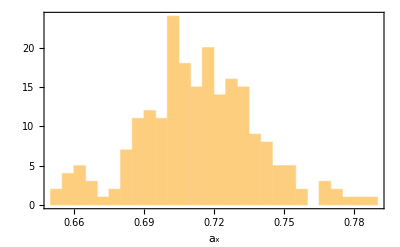

```mathematica
axtab=xtab-ytab;
{axmean=Mean[axtab],{sax=StandardDeviation[axtab],say=Mean[Diagonal[covmuz]^.5],say2=Median[Diagonal[covmuz]^.5]},saxmean=StandardDeviation[axtab]/Sqrt[Length[axtab]]}
5{sax,say,say2}
Histogram[axtab,{.005},PlotRange->All,Frame->True,FrameLabel->{"a_x"}]
```

```mathematica
axmeanz=Total[inVcovmuz.axtab]/Total[inVcovmuz,Infinity];
saz=(1/Total[inVcovmuz,Infinity])^.5;
{axmeanz,saz}
{axR16,saxR16}={0.71273,0.00176}(* aB = 0.71273 ± 0.00176 from Riess_2016_ApJ_826_56 1604.01424 *)
(axmeanz-axR16)/saxR16
```

{0.712725,0.00177556}

{0.71273,0.00176}

-0.00297924

```mathematica
chi2a[aa_]:=Total[(ytab-(xtab-aa))^2/Diagonal[covmuz]];
fma=FindMinimum[chi2a[aa],{aa,0.7}]
fma[[1]]/(Length[xtab]-1)
yf[x_]:=x-fma[[2,1,2]];
yfR16[x_]:=x-axR16;
```

{187.796,{aa→0.712725}}

0.869425

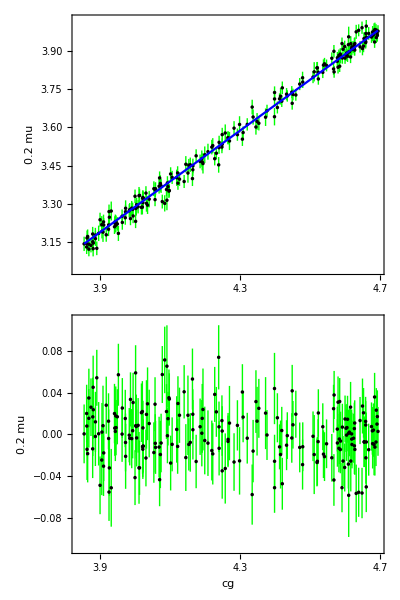

plots/hubble_diagram5-dm.pdf

```mathematica
mvec1=Table[Around[ytab[[n]],covmuz[[n,n]]^.5],{n,Length[ytab]}];
mvec2=Table[Around[yf[xtab[[n]]]-ytab[[n]],covmuz[[n,n]]^.5],{n,Length[ytab]}];
mvec3=Table[yfR16[xtab[[n]]]-ytab[[n]],{n,Length[ytab]}];
dataplot1=Thread[{xtab,mvec1}];
dataplot2=Thread[{xtab,mvec2}];
dataplot3=Thread[{xtab,mvec3}];

popo1=ListPlot[dataplot1,PlotRange->All,PlotStyle->Directive[PointSize[0.005],Black],IntervalMarkers->"Bars",IntervalMarkersStyle->Green,Frame->True,FrameStyle->15,FrameLabel->{None,"0.2 mu"}];
popo1=Show[popo1,Plot[yf[x],{x,Min[xtab],Max[xtab]},PlotStyle->Blue],FrameTicksStyle->{Automatic,{Directive[Black,.001],Automatic}},FrameTicks->{{Automatic,None},{Table[i,{i,3.5,5,.1}],None}},ImageSize->{500,400},AspectRatio->Full,ImagePadding->{{70,10},{All,All}}];
popo2=ListPlot[dataplot2,PlotStyle->Directive[PointSize[0.005],Black],IntervalMarkers->"Bars"(*"Fences"*)(*"Ellipses"*)(*"Bars"*),IntervalMarkersStyle->Green,Frame->True,FrameStyle->15,ImageSize->{500,200},AspectRatio->Full,FrameLabel->{"cg","0.2 mu"},FrameTicks->{{Automatic,None},{Table[i,{i,3.5,5,.1}],None}},PlotRange->{All,{-.11,.11}},ImagePadding->{{70,10},{All,All}}];
popot=Column[{popo1,popo2}]
Export["plots/hubble_diagram5-dm.pdf",popot]
```

### Pantheon

```mathematica
(* Pantheon data from arXiv:1710.00845 *)
dataset="pantheon";
Dimensions[datax=Import["data/Pantheon-lowz.txt","Table","HeaderLines"->0]];
data=datax[[2;;]];
ztab=data[[All,2]];
mutab=data[[All,5]];
TableForm[data[[;;5]],TableHeadings->{None, datax[[1]]}]

CovImp=Flatten[Import["data/Pantheon-lowz-cov.txt","Table"]];
Nsn=CovImp[[1]];
Dimensions[covmu=Partition[CovImp[[2;;]],Nsn]];
covmu=covmu+DiagonalMatrix[data[[All,6]]^2];
inVcovmu=Inverse[covmu];
Row[{"{z_min,z_max}=",MinMax[data[[All,2]]]}]
```

#name | zcmb | zhel | dz | mb | dmb | x1 | dx1 | color | dcolor | 3rdvar | d3rdvar | cov_m_s | cov_m_c | cov_s_c | set | ra | dec
06D2fb | 0.12531 | 0.12531 | 0. | 19.4684 | 0.10355 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
744 | 0.12679 | 0.12679 | 0. | 19.5429 | 0.11965 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1241 | 0.08859 | 0.08859 | 0. | 18.6435 | 0.10605 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1371 | 0.11782 | 0.11782 | 0. | 19.1935 | 0.0991 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1794 | 0.14055 | 0.14055 | 0. | 19.871 | 0.11635 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

{z_min,z_max}={0.02348,0.14949}

## calibration prior on M_B

```mathematica
(* the computation of the prior on MB needs the following quantities *)
Dimensions[inVcovmu]
{Nsn,Length[mutab],Length[ztab]}
```

{237,237}

{237,237,237}

```mathematica
(* fiducial values adopted by SH0ES *)
{q0fid,j0fid}={-0.55,1};

type=3; (* choose the measurements [km/s/Mpc] *)
{H0,sigH0}=Which[
type==1,
Print["Riess_2019_ApJ_876_85"];
{74.03,1.42}
,
type==2,
Print["Reid_2019_ApJL_886_L27"];
{73.5,1.4}
,
type==3,
Print["Riess_2020 2012.08534"];
{73.2,1.3}
];
```

Riess_2020 2012.08534

```mathematica
(* intercepts, its error and auxiliary quantities *)
ones=ConstantArray[1,Nsn];
Sum00=ones.inVcovmu.ones;
vecmoi=mutab-mB[ztab,1,q0fid,j0fid,0]; (* putting M-5Log10[H0] to zero *)
Sum10=vecmoi.inVcovmu.ones;

{axmeanz=-Sum10/(5Sum00)-5,saz=1/(5Sum00^.5)}
```

{0.712997,0.00193443}

### method 1 - demarginalization

```mathematica
muln[Mp_,sigM_,S0_,S1_]:=Log[10]/5 ( Mp - S1/S0+(1/S0+ sigM^2) Log[10]/5);
sigln[sigM_,S0_]:=Log[10]/5 √(1/S0+sigM^2) ;
meanH[Mp_,sigM_,S0_,S1_]:=ⅇ^(muln[Mp,sigM,S0,S1]+sigln[sigM,S0]^2/2);
varH[Mp_,sigM_,S0_,S1_]:=ⅇ^(2 muln[Mp,sigM,S0,S1]+sigln[sigM,S0]^2) (-1+ⅇ^(sigln[sigM,S0]^2));
skew[Mp_,sigM_,S0_]:=√(-1+ⅇ^(sigln[sigM,S0]^2)) (2+ⅇ^(sigln[sigM,S0]^2));
```

```mathematica
root=FindRoot[{meanH[Mp,sigM,Sum00,Sum10],varH[Mp,sigM,Sum00,Sum10]}=={H0,sigH0^2},{{Mp,-19},{sigM,0.04}}];
Row[{"Calibration prior on M_B: ",root}]

MpP=root[[1,2]];
sigMpP=root[[2,2]];
skew[MpP,sigMpP,Sum00];
```

Calibration prior on M_B: {Mp→-19.2435,sigM→0.0373286}

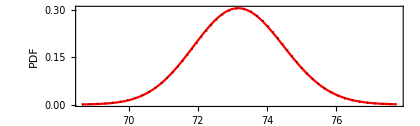

plots/pantheon-t3-postH-demarginalization.pdf

```mathematica
po=Plot[{PDF[LogNormalDistribution[muln[MpP,sigMpP,Sum00,Sum10],sigln[sigMpP,Sum00]],h],PDF[NormalDistribution[H0,sigH0],h]},{h,H0-3.5sigH0,H0+3.5sigH0},Frame->True,PlotStyle->{{Thick,Red},{ Dotted,Black}},FrameStyle->16,AspectRatio->.3, FrameLabel->{"H_0 (km s^-1 Mpc^-1)","PDF"},PlotLegends->Placed[{"Reconstruction (lognormal)","Target (Gaussian)"},Above(*{Left,Top}*)],ImageSize->420]
Export["plots/"<>dataset<>"-t"<>ToString[type]<>"-postH-demarginalization.pdf",po]
```

### method 2 - error propagation

-Graphics-

```mathematica
{Mx=5 (Log10[H0]-axmeanz-5),sMx=√((5/Log[10] sigH0/H0)^2-25saz^2)}
```

{-19.2424,0.0373318}

### method 3 - deconvolution

```mathematica
fh[h_,μ_,σ_]:=1/(h √(2 π) σ)Exp[-(Log[h]-μ)^2/(2 σ^2)];
mup[μ_,σ_]:=ⅇ^(μ+σ^2/2);
si2p[μ_,σ_]:=ⅇ^(2 μ+σ^2) (-1+ⅇ^(σ^2));
mulo[Mp_,ax_]:=Log[10]/5(Mp+5 ax+25);
silo[sMp_,sax_]:=Log[10]/5 √(sMp^2+25 sax^2);
```

```mathematica
root2=FindRoot[{mup[mulo[Mp,axmeanz],silo[sMp,saz]],si2p[mulo[Mp,axmeanz],silo[sMp,saz]]}=={H0,sigH0^2},{{Mp,-19},{sMp,0.04}}];
MpP2=root2[[1,2]];
sigMpP2=root2[[2,2]];
Row[{"Calibration prior on M_B: ",root2}]
```

Calibration prior on M_B: {Mp→-19.2428,sMp→0.0373286}

```mathematica
po=Plot[{fh[h,mulo[MpP2,axmeanz],silo[sigMpP2,saz]],PDF[NormalDistribution[H0,sigH0],h]},{h,H0-3.5sigH0,H0+3.5sigH0},Frame->True,PlotStyle->{{Thick,Red},{ Dotted,Black}},FrameStyle->16,AspectRatio->.3, FrameLabel->{"H_0 (km s^-1 Mpc^-1)","PDF"},PlotLegends->Placed[{"Reconstruction (lognormal)","Target (Gaussian)"},Above(*{Left,Top}*)],ImageSize->420]
Export["plots/"<>dataset<>"-t"<>ToString[type]<>"-postH-deconvolution.pdf",po]
```

-Graphics-

plots/pantheon-t3-postH-deconvolution.pdf

### table

```mathematica
Mfintab=Round[{{MpP,sigMpP},{Mx,sMx},{MpP2,sigMpP}},.0001];
tf=TableForm[Mfintab,TableHeadings->{{"Demarginalization","Error propagation","Deconvolution"}, {"M_B","σ_M"}}]
Export["plots/"<>dataset<>"-t"<>ToString[type]<>"-summary_tab.pdf",tf]
```

| M_B | σ_M
Demarginalization | -19.2435 | 0.0373
Error propagation | -19.2424 | 0.0373
Deconvolution | -19.2428 | 0.0373

plots/pantheon-t3-summary_tab.pdf